```mathematica
(*ONE-DIMENSIONAL CASE*)
```

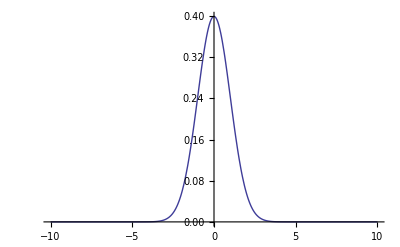

```mathematica
px[x_]:=PDF[NormalDistribution[0,1],x]
Plot[px[x],{x,-10,10}, PlotRange->All]
```

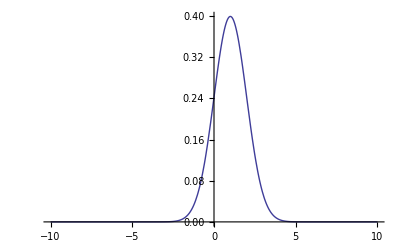

```mathematica
py[y_]:=PDF[NormalDistribution[1,1],y]
Plot[py[y],{y,-10,10}, PlotRange->All]
```

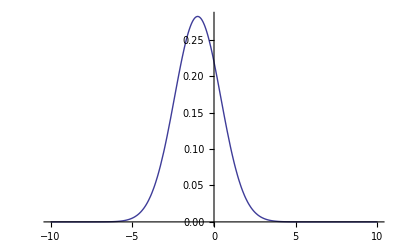

```mathematica
pm[dx_]:=NIntegrate[px[x]py[x-dx],{x,-10,10}]
Plot[pm[dx],{dx,-10,10}, PlotRange->All]
```

NIntegrate::inumr: The integrand ⅇ^-x^2/2 - 1/2\ (-1 + x + z)^2/2\ π has evaluated to non-numerical values for all sampling points in the region with boundaries {{-10, 10}}.

NIntegrate::inumr: The integrand ⅇ^-x^2/2 - 1/2\ (-1 + x - z)^2/2\ π has evaluated to non-numerical values for all sampling points in the region with boundaries {{-10, 10}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

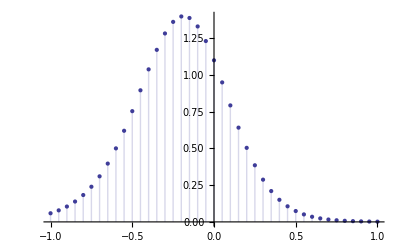

```mathematica
Clear[pd]
pd[n_]:=NIntegrate[pm[n*z]pz[z]z, {z,-10,10},MinRecursion->2,MaxRecursion->3];
x=Array[pd,41,{-1,1}];
n=Range[-1,1,0.05];
ListPlot[Thread[{n,x}],Filling->Axis]
(*ListPlot[Thread[{dz,pd}], Filling-> Axis]*)
(*NIntegrate gives an error when the integrand contains a parameter that does not have a numerical value, which in our case is dz. One way to get round the problem is to define an array for dz, and then evaluate pd[dz_] at each of those values, and then plot it*)
```